```mathematica
(*ref: Murphy, Fundamentals of light microscopy, p319*)
um=10^-6;
nm=10^-9;
λ=800 nm;
```

```mathematica
(*Diffraction limit. These eqs. are valid for NA > 0.7 *)
resXY[NA_]:=0.325 λ/(√2 NA^0.91)
resZ[RI_,NA_]:=0.532 λ/(√2)1/(RI-√(RI^2-NA^2))
```

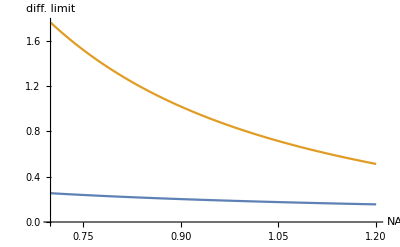

```mathematica
(*Resolution vs NA*)
RI=1.52;
Plot[{resXY[NA]/um,resZ[RI,NA]/um},{NA,0.7,1.2},AxesLabel->{"NA","diff. limit"}]
```

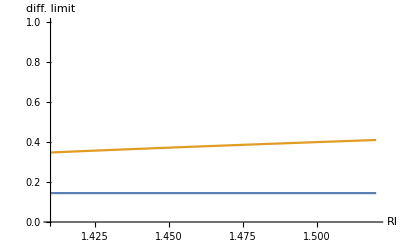

```mathematica
(*Resolution vs RI*)
NA=1.3;
Plot[{resXY[NA]/um,resZ[RI,NA]/um},{RI,1.41,1.52},PlotRange->{0,1},AxesLabel->{"RI","diff. limit"}]
```